## Te130

```mathematica
enData1=;
strData1=;
enData2=;
strData2=;
```

## Xe130

```mathematica
enData3=;
strData3=;
```

## Numerical params

```mathematica
elem[el_,n_]:=Style[Row[{Superscript["",n],StringTemplate["``"][el]}]];
xdp=0.325;
chi12=0.3;
el1=elem["Te",130];
el2=elem["Xe",130];
```

## Figures

### Figure1

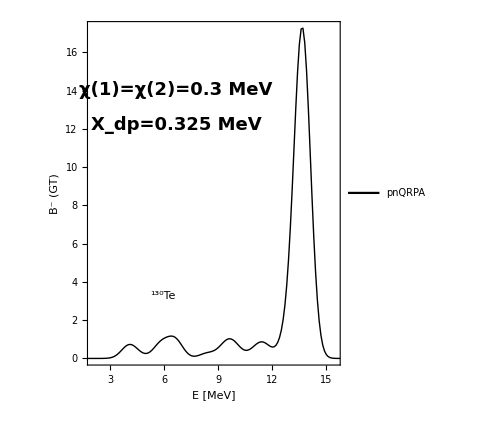

```mathematica
tableFig1=Table[{enData1[[i]],strData1[[i]]},{i,1,Length[strData1]}];
fig1=ListPlot[tableFig1,Joined->True,ImageSize->Medium,AspectRatio->1.2,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},PlotRange->{{2,15.5},Full},FrameLabel->{"E [MeV]","B^- (GT)"},LabelStyle->{20,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"pnQRPA"},{0.35,0.9}],Epilog->{Inset[Style[StringTemplate["χ(1)=χ(2)=`` MeV"][chi12],18,Bold,Black,FontFamily->"Times"],Scaled[{0.35,0.8}]],Inset[Style[StringTemplate["X_dp=`` MeV"][xdp],18,Bold,Black,FontFamily->"Times"],Scaled[{0.35,0.7}]],Inset[Framed[Style[el1,20,Bold,Black,FontFamily->"Times"]],Scaled[{0.3,0.2}]]}];
Show[fig1]
```

### Figure2

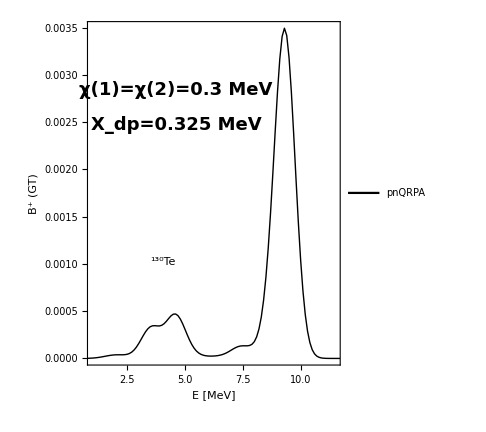

```mathematica
tableFig2=Table[{enData2[[i]],strData2[[i]]},{i,1,Length[strData2]}];
fig2=ListPlot[tableFig2,Joined->True,ImageSize->Medium,AspectRatio->1.2,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},PlotRange->{{1,11.5},Full},FrameLabel->{"E [MeV]","B^+ (GT)"},LabelStyle->{20,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"pnQRPA"},{0.35,0.9}],Epilog->{Inset[Style[StringTemplate["χ(1)=χ(2)=`` MeV"][chi12],18,Bold,Black,FontFamily->"Times"],Scaled[{0.35,0.8}]],Inset[Style[StringTemplate["X_dp=`` MeV"][xdp],18,Bold,Black,FontFamily->"Times"],Scaled[{0.35,0.7}]],Inset[Framed[Style[el1,20,Bold,Black,FontFamily->"Times"]],Scaled[{0.3,0.3}]]}];
Show[fig2]
```

### Figure3

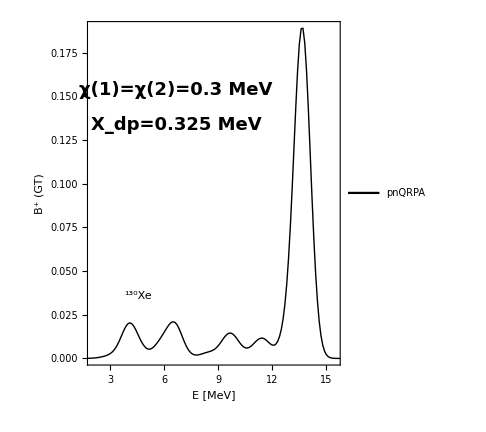

```mathematica
tableFig3=Table[{enData3[[i]],strData3[[i]]},{i,1,Length[strData3]}];
fig3=ListPlot[tableFig3,Joined->True,ImageSize->Medium,AspectRatio->1.2,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},PlotRange->{{2,15.5},Full},FrameLabel->{"E [MeV]","B^+ (GT)"},LabelStyle->{20,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"pnQRPA"},{0.35,0.9}],Epilog->{Inset[Style[StringTemplate["χ(1)=χ(2)=`` MeV"][chi12],18,Bold,Black,FontFamily->"Times"],Scaled[{0.35,0.8}]],Inset[Style[StringTemplate["X_dp=`` MeV"][xdp],18,Bold,Black,FontFamily->"Times"],Scaled[{0.35,0.7}]],Inset[Framed[Style[el2,20,Bold,Black,FontFamily->"Times"]],Scaled[{0.2,0.2}]]}];
Show[fig3]
```